```mathematica
config={A->1,Ts->1/100,f0->100/20,σ->0.2}
```

{A→1,Ts→1/100,f0→5,σ→0.2}

```mathematica
x[t_]=A*Exp[-t^2/(2σ^2)]*Cos[2Pi*f0*t]/.config
```

ⅇ^(-12.5 t^2) Cos[10 π t]

```mathematica
xd0[n_]=x[n*Ts]/.config
```

ⅇ^(-0.00125 n^2) Cos[(n π)/10]

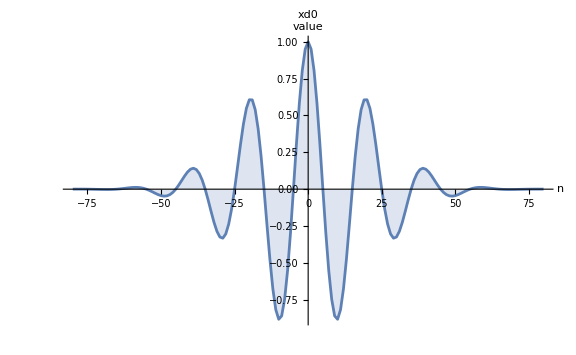

```mathematica
Block[{N0=1/(f0*Ts)/.config},
DiscretePlot[xd0[n],{n,-4N0,4N0},PlotRange->Full,PlotLabel->"xd0",AxesLabel->{"n","value"},ImageSize->Large]
]
```

```mathematica
X0[f_]=Block[{Ts=Ts/.config,σ=σ/.config},
Sum[xd0[n]*Exp[-I*2Pi*f*n*Ts],{n,-5σ/Ts,5σ/Ts}]
];
tilde X0[f_]=X0[f/Ts]/.config;
```

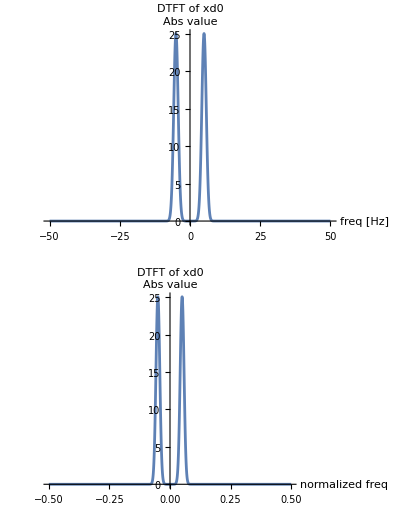

```mathematica
Block[{Ts=Ts/.config,p1,p2},
p1=Plot[Abs[X0[f]],{f,-1/(2Ts),1/(2Ts)},PlotRange->Full,PlotLabel->"DTFT of xd0",AxesLabel->{"freq [Hz]","Abs value"},ImageSize->Large];
p2=Plot[Abs[tilde X0[f]],{f,-1/2,1/2},PlotRange->Full,PlotLabel->"DTFT of xd0",AxesLabel->{"normalized freq","Abs value"},ImageSize->Large];
GraphicsGrid[{{p1},{p2}}]
]
```

```mathematica
xd1[n_]=xd0[2n];
```

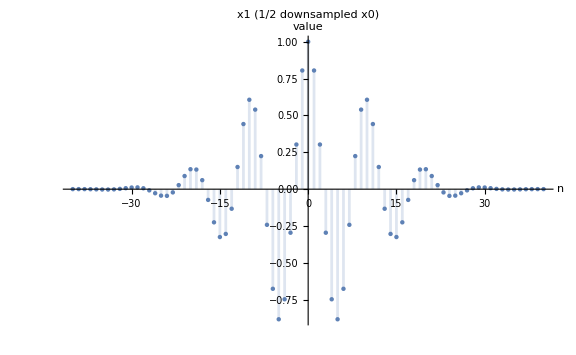

```mathematica
Block[{N0=1/(f0*2*Ts)/.config},
DiscretePlot[xd1[n],{n,-4N0,4N0},PlotRange->Full,PlotLabel->"x1 (1/2 downsampled x0)", AxesLabel->{"n","value"},ImageSize->Large]
]
```

```mathematica
X1[f_]=Block[{Ts=Ts/.config,σ=σ/.config},
Sum[xd1[n]*Exp[-I*2Pi*f*n*(2Ts)],{n,-(5/2)σ/Ts,(5/2)σ/Ts}]
];
tilde X1[f_]=X1[f/(2Ts)]/.config;
```

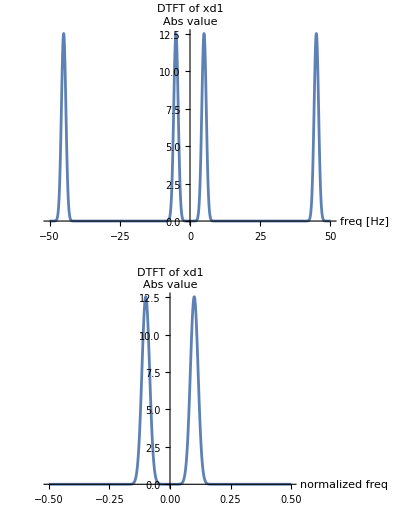

```mathematica
Block[{Ts=Ts/.config,p1,p2},
p1=Plot[Abs[X1[f]],{f,-1/(2Ts),1/(2Ts)},PlotRange->Full,PlotLabel->"DTFT of xd1",AxesLabel->{"freq [Hz]","Abs value"},ImageSize->Large];
p2=Plot[Abs[tilde X1[f]],{f,-1/2,1/2},PlotRange->Full,PlotLabel->"DTFT of xd1",AxesLabel->{"normalized freq","Abs value"},ImageSize->Large];
GraphicsGrid[{{p1},{p2}}]
]
```